```mathematica
solids =Import["Documents//LBM/LBM2d/samples/shear_test/solid_points.txt", "CSV"];
surface =Import["Documents//LBM/LBM2d/samples/shear_test/surface.txt", "CSV"];
reflection =Import["Documents//LBM/LBM2d/samples/shear_test/refl_points.txt", "CSV"];
streamfrom =Import["Documents//LBM/LBM2d/samples/shear_test/stream_from.txt", "CSV"];
streamto =Import["Documents//LBM/LBM2d/samples/shear_test/stream_to.txt", "CSV"];
bounce =Import["Documents//LBM/LBM2d/samples/shear_test/bounce_back.txt", "CSV"];
```

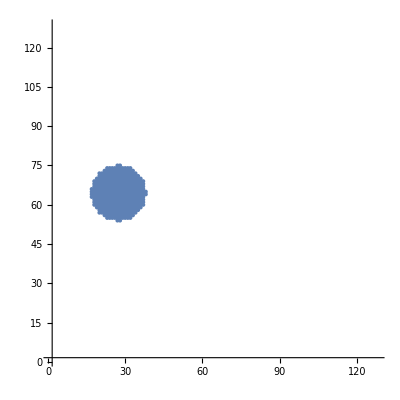

```mathematica
solidpoints=ListPlot[solids, PlotRange->{{1,128},{1,128}},AspectRatio->1 ];
surfacepoints=ListPlot[surface,PlotStyle->Red, PlotRange->{{1,128},{1,128}},AspectRatio->1 ];
reflpoints=ListPlot[reflection,PlotStyle->Purple, PlotRange->{{1,128},{1,128}},AspectRatio->1 ];
streaminit=ListPlot[streamfrom,PlotStyle->Orange, PlotRange->{{1,128},{1,128}},AspectRatio->1,PlotMarkers->"*" ];
streamfinal=ListPlot[streamto,PlotStyle->Green, PlotRange->{{1,128},{1,128}},AspectRatio->1 ];
bounceback=ListPlot[bounce,PlotStyle->Yellow, PlotRange->{{1,128},{1,128}},AspectRatio->1, PlotMarkers->"+"];

Show[solidpoints]
```

```mathematica
Export["/home/noemi/Documents/LBM/LBM2d/samples/shear_test/bounce.eps",%525,"EPS"]
```

/home/noemi/Documents/LBM/LBM2d/samples/shear_test/bounce.eps

```mathematica
Export["/home/noemi/Documents/LBM/LBM2d/samples/shear_test/bounce.eps",%511,"EPS"]
```

/home/noemi/Documents/LBM/LBM2d/samples/shear_test/bounce.eps